# Phase Transition for (SU(2))_R in Type-I 2HDM Model

## Effective Potential

### Tree level

Take the 2HDM model for both left and right Higgs. The right-handed Higgs tree-level potential without self-interacting is:

```mathematica
$Assumptions={{ρ,α,θ,μR,κ,δ,λR,h1,h2,h3,g,gy,ytp,x1r,x1i,y1r,y1i,x2r,x2i,y2r,y2i}∈PositiveReals};
(*Global assumptions for the parameters*)
VR=Tr[-μR^2(Φ1†.Φ1 +Φ2†.Φ2)-κ ⅇ^(ⅈ δ)Φ1†.Φ2 - κ ⅇ^(-ⅈ δ)Φ2†.Φ1 + λR/2((Φ1†.Φ1)^2+(Φ2†.Φ2)^2)+h1 (Φ1†.Φ2)(Φ2†.Φ1)+h2(Φ1†.Φ1)(Φ2†.Φ2)+h3((Φ1†.Φ2)^2+(Φ2†.Φ1)^2)];
```

All the parameters here are real. The Φ1 and Φ2 are the two Higgs field in H_R. We should assume that the symmetry breaking scale v_Ris much higher than the EW scale so that the gauge bosons can fit the LHC bounds. 
Based on this assumption, we can take simply H_L→0 when calculating the effective potential for H_R. i.e. We assume there is only H_R in the tree level field. So the above equation is just the tree-level contribution.
In general, the Higgs field can be written as:

```mathematica
Φ1=1/(√2)({{ϕ1p}, {ϕ10}});
Φ2=1/(√2)({{ϕ2p}, {ϕ20}});
```

After ssb, the Higgs field should be of the form:

```mathematica
ssb={ϕ1p->0,ϕ10->ρ ⅇ^(ⅈ(α+θ)/2),ϕ2p->0,ϕ20->ρ ⅇ^(ⅈ(α-θ)/2)};
Φ1/.ssb//MatrixForm
Φ2/.ssb//MatrixForm
```

(0
(ⅇ^(1/2 ⅈ (α+θ)) ρ)/(√2))

(0
(ⅇ^(1/2 ⅈ (α-θ)) ρ)/(√2))

Then we can get the tree-level potential V_tree(ρ,θ):

```mathematica
Vtree=VR/.ssb//FullSimplify
```

1/4 ρ^2 (-4 μR^2+(h1+h2+λR) ρ^2-4 κ Cos[δ-θ]+2 h3 ρ^2 Cos[2 θ])

### Coleman-Weinberg 1-loop Correction

From now on we focuses on the corrections for the effective potential. As a preparation, we should at first figure out the mass spectrum for this model.

#### Gauge boson and Fermion masses

Only the field Φ_2 couples to the fermions. The heaviest contribution comes from the extra quark and lepton from the term (Q̄)_3 H_R t' and (L̄)_3 H_R^†τ'. Notice that the SM top quark does not couple to H_Rsince the right-handed top quark is singlet under (SU(2))_R, and similar for the tau lepton. Here we assume that the extra quark is heavier than all the other SM quarks, the extra lepton is heavier than all the other leptons. We also assume that the extra quark t' is much heavier than the lepton. Thus we only include the heavy extra quark into the contributions for the effective potential. The field-dependent mass for this extra quark is (the corresponding Yukawa coupling constant is yt`):

```mathematica
mtp[ρ_]:=1/2 ytp^2 ρ^2;
```

The gauge bosons W_R and Z_Ralso contribute to the effective potential. These bosons couple with both of the fields in H_R. So the field-dependent mass-square for the gauge bosons are:

```mathematica
mWR[ρ_]:=g^2/2 ρ^2;
mZR[ρ_]:=(g^2+gy^2)/2 ρ^2;
```

#### Higgs mass spectrum

The tree-level Higgs mass is defined as the second-order derivative for all the degree of freedom of fields in these Higgs doublets. To be more physical, let us parameterize the Higgs field in the following parametrization:

```mathematica
param={ϕ1p->x1r+ⅈ x1i,ϕ10->y1r+ⅈ y1i,ϕ2p->x2r+ⅈ x2i,ϕ20->y2r+ⅈ y2i};
Φ1p=Φ1/.param//MatrixForm
Φ2p=Φ2/.param//MatrixForm
```

((ⅈ x1i+x1r)/(√2)
(ⅈ y1i+y1r)/(√2))

((ⅈ x2i+x2r)/(√2)
(ⅈ y2i+y2r)/(√2))

Plug in the potential expressions, we can write down the potential in this parametrization.

```mathematica
Vnormal=VR/.param//FullSimplify
```

1/8 (2 h1 ((x1i+ⅈ x1r) (x2i-ⅈ x2r)+(y1i+ⅈ y1r) (y2i-ⅈ y2r)) ((x1i-ⅈ x1r) (x2i+ⅈ x2r)+(y1i-ⅈ y1r) (y2i+ⅈ y2r))+2 h2 (x1i^2+x1r^2+y1i^2+y1r^2) (x2i^2+x2r^2+y2i^2+y2r^2)+4 h3 (x1r (-x2i+x2r)+x1i (x2i+x2r)+y1r (-y2i+y2r)+y1i (y2i+y2r)) (x1i (x2i-x2r)+x1r (x2i+x2r)+y1i (y2i-y2r)+y1r (y2i+y2r))-4 ⅇ^(ⅈ δ) ((x1i+ⅈ x1r) (x2i-ⅈ x2r)+(y1i+ⅈ y1r) (y2i-ⅈ y2r)) κ-4 ⅇ^(-ⅈ δ) ((x1i-ⅈ x1r) (x2i+ⅈ x2r)+(y1i-ⅈ y1r) (y2i+ⅈ y2r)) κ+((x1i^2+x1r^2+y1i^2+y1r^2)^2+(x2i^2+x2r^2+y2i^2+y2r^2)^2) λR-4 (x1i^2+x1r^2+x2i^2+x2r^2+y1i^2+y1r^2+y2i^2+y2r^2) μR^2)

It should be equal to the tree level potential when only the real part of the lower component is zero:

```mathematica
Vnormal/.{x1r->0,x1i->0,y1r->ρ,y1i->0,x2r->0,x2i->0,y2r->ρ,y2i->0,δ->0}//FullSimplify
Vtree/.{δ->0,θ->0}//FullSimplify
```

-(κ+μR^2) ρ^2+1/4 (h1+h2+2 h3+λR) ρ^4

-(κ+μR^2) ρ^2+1/4 (h1+h2+2 h3+λR) ρ^4

The mass matrix is defined as

m_ab=(∂^2 V)/(∂ϕ_a∂ϕ_b)

calculate:

```mathematica
variables={x1r,x1i,y1r,y1i,x2r,x2i,y2r,y2i};
DVnormal=D[Vnormal,{variables}];
DDVnormal=D[DVnormal,{variables}];
DDVnormal//FullSimplify//MatrixForm
```

(1/2 (2 h3 (-x2i^2+x2r^2)+h1 (x2i^2+x2r^2)+h2 (x2i^2+x2r^2+y2i^2+y2r^2)+(x1i^2+3 x1r^2+y1i^2+y1r^2) λR-2 μR^2) | 2 h3 x2i x2r+x1i x1r λR | 1/2 ((h1-2 h3) x2i y2i+(h1+2 h3) x2r y2r+2 x1r y1r λR) | h3 x2r y2i+h3 x2i y2r+1/2 h1 (x2r y2i-x2i y2r)+x1r y1i λR | h2 x1r x2r+1/2 h1 (2 x1r x2r+y1i y2i+y1r y2r)+h3 (2 x1i x2i+2 x1r x2r+y1i y2i+y1r y2r)-κ Cos[δ] | h2 x1r x2i+1/2 h1 (2 x1r x2i+y1r y2i-y1i y2r)+h3 (-2 x1r x2i+2 x1i x2r-y1r y2i+y1i y2r)+κ Sin[δ] | h3 x2i y1i+h3 x2r y1r+1/2 h1 (-x2i y1i+x2r y1r)+h2 x1r y2r | 1/2 ((h1+2 h3) x2r y1i+(h1-2 h3) x2i y1r+2 h2 x1r y2i)
2 h3 x2i x2r+x1i x1r λR | 1/2 (2 h3 (x2i-x2r) (x2i+x2r)+h1 (x2i^2+x2r^2)+h2 (x2i^2+x2r^2+y2i^2+y2r^2)+(3 x1i^2+x1r^2+y1i^2+y1r^2) λR-2 μR^2) | h3 x2r y2i+h3 x2i y2r+1/2 h1 (-x2r y2i+x2i y2r)+x1i y1r λR | 1/2 ((h1+2 h3) x2i y2i+(h1-2 h3) x2r y2r+2 x1i y1i λR) | h2 x1i x2r+h3 (2 x1r x2i-2 x1i x2r+y1r y2i-y1i y2r)+1/2 h1 (2 x1i x2r-y1r y2i+y1i y2r)-κ Sin[δ] | h2 x1i x2i+1/2 h1 (2 x1i x2i+y1i y2i+y1r y2r)+h3 (2 x1i x2i+2 x1r x2r+y1i y2i+y1r y2r)-κ Cos[δ] | 1/2 ((h1-2 h3) x2r y1i+(h1+2 h3) x2i y1r+2 h2 x1i y2r) | h3 x2i y1i+h3 x2r y1r+1/2 h1 (x2i y1i-x2r y1r)+h2 x1i y2i
1/2 ((h1-2 h3) x2i y2i+(h1+2 h3) x2r y2r+2 x1r y1r λR) | h3 x2r y2i+h3 x2i y2r+1/2 h1 (-x2r y2i+x2i y2r)+x1i y1r λR | 1/2 (2 h3 (-y2i^2+y2r^2)+h1 (y2i^2+y2r^2)+h2 (x2i^2+x2r^2+y2i^2+y2r^2)+(x1i^2+x1r^2+y1i^2+3 y1r^2) λR-2 μR^2) | 2 h3 y2i y2r+y1i y1r λR | h2 x2r y1r+1/2 h1 (-x1i y2i+x1r y2r)+h3 (x1i y2i+x1r y2r) | 1/2 (2 h2 x2i y1r+(h1-2 h3) x1r y2i+(h1+2 h3) x1i y2r) | h2 y1r y2r+1/2 h1 (x1i x2i+x1r x2r+2 y1r y2r)+h3 (x1i x2i+x1r x2r+2 y1i y2i+2 y1r y2r)-κ Cos[δ] | h2 y1r y2i+1/2 h1 (x1r x2i-x1i x2r+2 y1r y2i)+h3 (-x1r x2i+x1i x2r-2 y1r y2i+2 y1i y2r)+κ Sin[δ]
h3 x2r y2i+h3 x2i y2r+1/2 h1 (x2r y2i-x2i y2r)+x1r y1i λR | 1/2 ((h1+2 h3) x2i y2i+(h1-2 h3) x2r y2r+2 x1i y1i λR) | 2 h3 y2i y2r+y1i y1r λR | 1/2 (2 h3 (y2i-y2r) (y2i+y2r)+h1 (y2i^2+y2r^2)+h2 (x2i^2+x2r^2+y2i^2+y2r^2)+(x1i^2+x1r^2+3 y1i^2+y1r^2) λR-2 μR^2) | 1/2 (2 h2 x2r y1i+(h1+2 h3) x1r y2i+(h1-2 h3) x1i y2r) | h2 x2i y1i+1/2 h1 (x1i y2i-x1r y2r)+h3 (x1i y2i+x1r y2r) | -1/2 (h1-2 h3) (x1r x2i-x1i x2r)+2 h3 y1r y2i+(h1+h2-2 h3) y1i y2r-κ Sin[δ] | h2 y1i y2i+1/2 h1 (x1i x2i+x1r x2r+2 y1i y2i)+h3 (x1i x2i+x1r x2r+2 y1i y2i+2 y1r y2r)-κ Cos[δ]
h2 x1r x2r+1/2 h1 (2 x1r x2r+y1i y2i+y1r y2r)+h3 (2 x1i x2i+2 x1r x2r+y1i y2i+y1r y2r)-κ Cos[δ] | h2 x1i x2r+h3 (2 x1r x2i-2 x1i x2r+y1r y2i-y1i y2r)+1/2 h1 (2 x1i x2r-y1r y2i+y1i y2r)-κ Sin[δ] | h2 x2r y1r+1/2 h1 (-x1i y2i+x1r y2r)+h3 (x1i y2i+x1r y2r) | 1/2 (2 h2 x2r y1i+(h1+2 h3) x1r y2i+(h1-2 h3) x1i y2r) | 1/2 (2 h3 (-x1i^2+x1r^2)+h1 (x1i^2+x1r^2)+h2 (x1i^2+x1r^2+y1i^2+y1r^2)+(x2i^2+3 x2r^2+y2i^2+y2r^2) λR-2 μR^2) | 2 h3 x1i x1r+x2i x2r λR | 1/2 ((h1-2 h3) x1i y1i+(h1+2 h3) x1r y1r+2 x2r y2r λR) | h3 x1r y1i+h3 x1i y1r+1/2 h1 (x1r y1i-x1i y1r)+x2r y2i λR
h2 x1r x2i+1/2 h1 (2 x1r x2i+y1r y2i-y1i y2r)+h3 (-2 x1r x2i+2 x1i x2r-y1r y2i+y1i y2r)+κ Sin[δ] | h2 x1i x2i+1/2 h1 (2 x1i x2i+y1i y2i+y1r y2r)+h3 (2 x1i x2i+2 x1r x2r+y1i y2i+y1r y2r)-κ Cos[δ] | 1/2 (2 h2 x2i y1r+(h1-2 h3) x1r y2i+(h1+2 h3) x1i y2r) | h2 x2i y1i+1/2 h1 (x1i y2i-x1r y2r)+h3 (x1i y2i+x1r y2r) | 2 h3 x1i x1r+x2i x2r λR | 1/2 (2 h3 (x1i-x1r) (x1i+x1r)+h1 (x1i^2+x1r^2)+h2 (x1i^2+x1r^2+y1i^2+y1r^2)+(3 x2i^2+x2r^2+y2i^2+y2r^2) λR-2 μR^2) | h3 x1r y1i+h3 x1i y1r+1/2 h1 (-x1r y1i+x1i y1r)+x2i y2r λR | 1/2 ((h1+2 h3) x1i y1i+(h1-2 h3) x1r y1r+2 x2i y2i λR)
h3 x2i y1i+h3 x2r y1r+1/2 h1 (-x2i y1i+x2r y1r)+h2 x1r y2r | 1/2 ((h1-2 h3) x2r y1i+(h1+2 h3) x2i y1r+2 h2 x1i y2r) | h2 y1r y2r+1/2 h1 (x1i x2i+x1r x2r+2 y1r y2r)+h3 (x1i x2i+x1r x2r+2 y1i y2i+2 y1r y2r)-κ Cos[δ] | -1/2 (h1-2 h3) (x1r x2i-x1i x2r)+2 h3 y1r y2i+(h1+h2-2 h3) y1i y2r-κ Sin[δ] | 1/2 ((h1-2 h3) x1i y1i+(h1+2 h3) x1r y1r+2 x2r y2r λR) | h3 x1r y1i+h3 x1i y1r+1/2 h1 (-x1r y1i+x1i y1r)+x2i y2r λR | 1/2 (2 h3 (-y1i^2+y1r^2)+h1 (y1i^2+y1r^2)+h2 (x1i^2+x1r^2+y1i^2+y1r^2)+(x2i^2+x2r^2+y2i^2+3 y2r^2) λR-2 μR^2) | 2 h3 y1i y1r+y2i y2r λR
1/2 ((h1+2 h3) x2r y1i+(h1-2 h3) x2i y1r+2 h2 x1r y2i) | h3 x2i y1i+h3 x2r y1r+1/2 h1 (x2i y1i-x2r y1r)+h2 x1i y2i | h2 y1r y2i+1/2 h1 (x1r x2i-x1i x2r+2 y1r y2i)+h3 (-x1r x2i+x1i x2r-2 y1r y2i+2 y1i y2r)+κ Sin[δ] | h2 y1i y2i+1/2 h1 (x1i x2i+x1r x2r+2 y1i y2i)+h3 (x1i x2i+x1r x2r+2 y1i y2i+2 y1r y2r)-κ Cos[δ] | h3 x1r y1i+h3 x1i y1r+1/2 h1 (x1r y1i-x1i y1r)+x2r y2i λR | 1/2 ((h1+2 h3) x1i y1i+(h1-2 h3) x1r y1r+2 x2i y2i λR) | 2 h3 y1i y1r+y2i y2r λR | 1/2 (2 h3 (y1i-y1r) (y1i+y1r)+h1 (y1i^2+y1r^2)+h2 (x1i^2+x1r^2+y1i^2+y1r^2)+(x2i^2+x2r^2+3 y2i^2+y2r^2) λR-2 μR^2))

This is not the final result. We should change the doublet into the correct form with correct vev. Thus we should apply:

```mathematica
correctvev={x1r->0,x1i->0,y1r->ρ,y1i->0,x2r->0,x2i->0,y2r->ρ,y2i->0,δ->0};
```

Then the mass matrix and the eigenvalues becomes:

```mathematica
Hmassmatrix=DDVnormal/.correctvev;
Hmassmatrix//FullSimplify//MatrixForm
Hmass=Eigenvalues[Hmassmatrix];
Hmass//FullSimplify//MatrixForm
```

(-μR^2+1/2 (h2+λR) ρ^2 | 0 | 0 | 0 | -κ+1/2 (h1+2 h3) ρ^2 | 0 | 0 | 0
0 | -μR^2+1/2 (h2+λR) ρ^2 | 0 | 0 | 0 | -κ+1/2 (h1+2 h3) ρ^2 | 0 | 0
0 | 0 | -μR^2+1/2 (h1+h2+2 h3+3 λR) ρ^2 | 0 | 0 | 0 | -κ+(h1+h2+2 h3) ρ^2 | 0
0 | 0 | 0 | -μR^2+1/2 (h1+h2-2 h3+λR) ρ^2 | 0 | 0 | 0 | -κ+2 h3 ρ^2
-κ+1/2 (h1+2 h3) ρ^2 | 0 | 0 | 0 | -μR^2+1/2 (h2+λR) ρ^2 | 0 | 0 | 0
0 | -κ+1/2 (h1+2 h3) ρ^2 | 0 | 0 | 0 | -μR^2+1/2 (h2+λR) ρ^2 | 0 | 0
0 | 0 | -κ+(h1+h2+2 h3) ρ^2 | 0 | 0 | 0 | -μR^2+1/2 (h1+h2+2 h3+3 λR) ρ^2 | 0
0 | 0 | 0 | -κ+2 h3 ρ^2 | 0 | 0 | 0 | -μR^2+1/2 (h1+h2-2 h3+λR) ρ^2)

(κ-μR^2+1/2 (h1+h2-6 h3+λR) ρ^2
κ-μR^2+1/2 (-h1+h2-2 h3+λR) ρ^2
κ-μR^2+1/2 (-h1+h2-2 h3+λR) ρ^2
-κ-μR^2+1/2 (h1+h2+2 h3+λR) ρ^2
-κ-μR^2+1/2 (h1+h2+2 h3+λR) ρ^2
-κ-μR^2+1/2 (h1+h2+2 h3+λR) ρ^2
κ-μR^2-1/2 (h1+h2+2 h3-3 λR) ρ^2
-κ-μR^2+3/2 (h1+h2+2 h3+λR) ρ^2)

These are the eigenvalues. However, there is another constraints that we should apply: we should make sure that the ρ is indeed the vev. i.e. we should impose that (∂V_tree)/(∂ρ)=0. This gives a constraint. Thus we can finalize calculating the field-dependent mass for the Higgs scalar sector in the limit that all the other fields except for the fields who get vev are 0.

```mathematica
equation=D[Vnormal/.correctvev,ρ]==0;
μRvalue=Solve[equation,μR][[1]]
Hmassfinal=Hmass/.μRvalue//FullSimplify;
Hmassfinal//MatrixForm
```

{μR→-(√(-2 κ+h1 ρ^2+h2 ρ^2+2 h3 ρ^2+λR ρ^2))/(√2)}

(2 (κ-2 h3 ρ^2)
2 κ-(h1+2 h3) ρ^2
2 κ-(h1+2 h3) ρ^2
0
0
0
2 κ-(h1+h2+2 h3-λR) ρ^2
(h1+h2+2 h3+λR) ρ^2)

This meets well with the 2HDM reviews: there should be 5 non-zero masses, two among which are degenerate.

#### Coleman-Weinberg Corrections: Result

With the mass spectrum calculated, we can figure out all of the corrections. The Potential is defined as:

V_CW=1/(64 π^2)[∑_scalars n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-3/2)+∑_(gauge bosons) n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-5/6)-∑_fermions n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-3/2)]

```mathematica
scalarmass=DeleteCases[Hmassfinal,0]
VCW=1/(64 π^2)Sum[scalarmass[[i]]^2*(Log[(Abs[scalarmass[[i]]]/Λ^2)]-3/2)  ,{i,1,Length[scalarmass]}]+1/(64 π^2)(3 mZR[ρ]^2(Log[mZR[ρ]/Λ^2]-5/6))+1/(64 π^2)(6 mWR[ρ]^2(Log[mWR[ρ]/Λ^2]-5/6))-1/(64 π^2)(2 mtp[ρ]^2(Log[mtp[ρ]/Λ^2]-3/2))//Simplify
```

{2 (κ-2 h3 ρ^2),2 κ-(h1+2 h3) ρ^2,2 κ-(h1+2 h3) ρ^2,2 κ-(h1+h2+2 h3-λR) ρ^2,(h1+h2+2 h3+λR) ρ^2}

1/(256 π^2)(g^4 ρ^4 (-5+6 Log[(g^2 ρ^2)/(2 Λ^2)])+3 (g^2+gy^2)^2 ρ^4 (-5/6+Log[((g^2+gy^2) ρ^2)/(2 Λ^2)])-ytp^4 ρ^4 (-3+2 Log[(ytp^2 ρ^2)/(2 Λ^2)])+2 (h1+h2+2 h3+λR)^2 ρ^4 (-3+2 Log[((h1+h2+2 h3+λR) ρ^2)/Λ^2])+8 (κ-2 h3 ρ^2)^2 (-3+2 Log[(2 Abs[κ-2 h3 ρ^2])/Λ^2])+8 (-2 κ+(h1+2 h3) ρ^2)^2 (-3/2+Log[Abs[2 κ-(h1+2 h3) ρ^2]/Λ^2])+4 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2 (-3/2+Log[Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]/Λ^2]))

Here, we take into account the Higgs, the W_R and Z_R bosons, and the extra quark.

### Finite-Temperature Corrections

The finite-temperature corrections are expressed as:

V_FT=T^4/(2 π^2)[∑J_B(m_i^2/T^2)-∑J_F(m_i^2/T^2)]

Here we use the expansion for the function J_B and J_F:

```mathematica
JB[x_]:=-π^4/45+π^2/12 x^2-π/6 x^3-1/32 x^4(Log[x^2]-5.4076);
JF[x_]:=-7 π^4/360-π^2/24 x^2-1/32 x^4(Log[x^2]-2.6351);
```

Lets calculate the corrections:

```mathematica
VFT=T^4/(2 π^2)(Sum[JB[(√Abs[scalarmass[[i]]])/T],{i,1,Length[scalarmass]}]+6JB[(√mWR[ρ])/T]+3JB[(√mZR[ρ])/T]-2JF[(√mtp[ρ])/T])//Simplify
```

-1.34336 T^4+0.1875 g^2 T^2 ρ^2+0.0625 gy^2 T^2 ρ^2+0.0208333 T^2 ytp^2 ρ^2+0.0416667 T^2 (h1+h2+2 h3+λR) ρ^2-0.0562698 g^3 T ρ^3-0.0281349 g^2 √(g^2+gy^2) T ρ^3-0.0281349 gy^2 √(g^2+gy^2) T ρ^3-0.0265258 T (h1+h2+2 h3+λR)^(3/2) ρ^3+0.0192623 g^4 ρ^4+0.0128415 g^2 gy^2 ρ^4+0.00642076 gy^4 ρ^4-0.00208587 ytp^4 ρ^4+0.00856101 (h1+h2+2 h3+λR)^2 ρ^4+0.034244 (κ-2. h3 ρ^2)^2+0.017122 (-2 κ+(h1+2 h3) ρ^2)^2+0.00856101 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2+0.0833333 T^2 Abs[κ-2 h3 ρ^2]-0.0750264 T Abs[κ-2 h3 ρ^2]^(3/2)+0.0833333 T^2 Abs[2 κ-(h1+2 h3) ρ^2]-0.0530516 T Abs[2 κ-(h1+2 h3) ρ^2]^(3/2)+0.0416667 T^2 Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]-0.0265258 T Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]^(3/2)-0.00237472 g^4 ρ^4 Log[(g^2 ρ^2)/(2 T^2)]-0.00118736 g^4 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]-0.00237472 g^2 gy^2 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]-0.00118736 gy^4 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]+0.000791572 ytp^4 ρ^4 Log[(ytp^2 ρ^2)/(2 T^2)]-0.00158314 (h1+h2+2 h3+λR)^2 ρ^4 Log[((h1+h2+2 h3+λR) ρ^2)/T^2]-0.00633257 (κ-2 h3 ρ^2)^2 Log[(2 Abs[κ-2 h3 ρ^2])/T^2]-0.00316629 (-2 κ+(h1+2 h3) ρ^2)^2 Log[Abs[2 κ-(h1+2 h3) ρ^2]/T^2]-0.00158314 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2 Log[Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]/T^2]

## Potential at Finite Temperatures: Plots and Phase Transition

In this section, we investigate the properties of the effective potential. Sum over all the previous result, we have:

```mathematica
Veff=Vtree+VCW+VFT
```

-1.34336 T^4+0.1875 g^2 T^2 ρ^2+0.0625 gy^2 T^2 ρ^2+0.0208333 T^2 ytp^2 ρ^2+0.0416667 T^2 (h1+h2+2 h3+λR) ρ^2-0.0562698 g^3 T ρ^3-0.0281349 g^2 √(g^2+gy^2) T ρ^3-0.0281349 gy^2 √(g^2+gy^2) T ρ^3-0.0265258 T (h1+h2+2 h3+λR)^(3/2) ρ^3+0.0192623 g^4 ρ^4+0.0128415 g^2 gy^2 ρ^4+0.00642076 gy^4 ρ^4-0.00208587 ytp^4 ρ^4+0.00856101 (h1+h2+2 h3+λR)^2 ρ^4+0.034244 (κ-2. h3 ρ^2)^2+0.017122 (-2 κ+(h1+2 h3) ρ^2)^2+0.00856101 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2+0.0833333 T^2 Abs[κ-2 h3 ρ^2]-0.0750264 T Abs[κ-2 h3 ρ^2]^(3/2)+0.0833333 T^2 Abs[2 κ-(h1+2 h3) ρ^2]-0.0530516 T Abs[2 κ-(h1+2 h3) ρ^2]^(3/2)+0.0416667 T^2 Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]-0.0265258 T Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]^(3/2)+1/4 ρ^2 (-4 μR^2+(h1+h2+λR) ρ^2-4 κ Cos[δ-θ]+2 h3 ρ^2 Cos[2 θ])-0.00237472 g^4 ρ^4 Log[(g^2 ρ^2)/(2 T^2)]-0.00118736 g^4 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]-0.00237472 g^2 gy^2 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]-0.00118736 gy^4 ρ^4 Log[(0.5 (g^2+gy^2) ρ^2)/T^2]+0.000791572 ytp^4 ρ^4 Log[(ytp^2 ρ^2)/(2 T^2)]-0.00158314 (h1+h2+2 h3+λR)^2 ρ^4 Log[((h1+h2+2 h3+λR) ρ^2)/T^2]-0.00633257 (κ-2 h3 ρ^2)^2 Log[(2 Abs[κ-2 h3 ρ^2])/T^2]-0.00316629 (-2 κ+(h1+2 h3) ρ^2)^2 Log[Abs[2 κ-(h1+2 h3) ρ^2]/T^2]-0.00158314 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2 Log[Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]/T^2]+1/(256 π^2)(g^4 ρ^4 (-5+6 Log[(g^2 ρ^2)/(2 Λ^2)])+3 (g^2+gy^2)^2 ρ^4 (-5/6+Log[((g^2+gy^2) ρ^2)/(2 Λ^2)])-ytp^4 ρ^4 (-3+2 Log[(ytp^2 ρ^2)/(2 Λ^2)])+2 (h1+h2+2 h3+λR)^2 ρ^4 (-3+2 Log[((h1+h2+2 h3+λR) ρ^2)/Λ^2])+8 (κ-2 h3 ρ^2)^2 (-3+2 Log[(2 Abs[κ-2 h3 ρ^2])/Λ^2])+8 (-2 κ+(h1+2 h3) ρ^2)^2 (-3/2+Log[Abs[2 κ-(h1+2 h3) ρ^2]/Λ^2])+4 (-2 κ+(h1+h2+2 h3-λR) ρ^2)^2 (-3/2+Log[Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]/Λ^2]))

Now try some parameters. We should fix the gauge couplings of the SM parameters and regard the other parameters in 2HDM are free.

```mathematica
SMparam={g->0.65,gy->0.36};
newparam={μR->2,κ->2,h1->0.005,h2->0.005,h3->0.005,λR->0.005,ytp->0.5};
scale={Λ->10,T->10};
```

Plots are shown here. In the first plot, we plot the tree-level potential and the potential with CW corrections.  If the two curves are very close to each other, then the corrections are reasonable. In the second plot, we plotted out the shape of the effective potential near the non-zero true vev. In the 3rd plot, we plot the higher temperature case, too see that the true vev is 0 when the temperature is higher. We see that the strong 1st order phase transition is possible. (For simplicity for analytical analysis, I personally suggest to discard the CW correction since this correction is too small.)

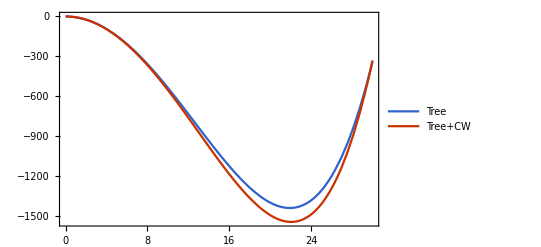

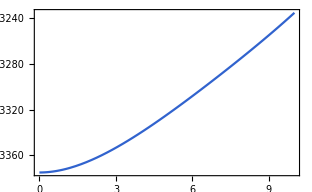

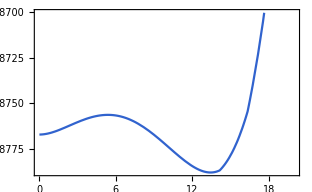

```mathematica
Vtreeparam=Vtree/.SMparam/.newparam/.scale/.{δ->0,θ->0};
VCWparam=VCW/.SMparam/.newparam/.scale/.{δ->0,θ->0};
Veffparam=Veff/.SMparam/.newparam/.scale/.{δ->0,θ->0};
Plot[{Vtreeparam,Vtreeparam+VCWparam},{ρ,0,30},PlotLegends->{"Tree","Tree+CW"}]
Plot[Veffparam,{ρ,0,10}]
Plot[Veff/.SMparam/.newparam/.{Λ->9,T->9}/.{δ->0,θ->0},{ρ,0,20}]
```

## Approximation Analysis

Here we write down the analytical expression for the parameter constraint for strong 1st order phase transition. From what we see before, the Coleman-Weinberg 1-loop correction is very small and does not depend on temperature. So in this section, we simply discard it. We still use the same tree-level potential:

```mathematica
Vtreeapr=Vtree/.{δ->0,θ->0};
Vtreeapr//FullSimplify
```

-(κ+μR^2) ρ^2+1/4 (h1+h2+2 h3+λR) ρ^4

For the finite-temperature corrections, we can simply discard the constant term. Logarithm term is also neglected. Now we re-define the function:

```mathematica
JBapr[x_]:=π^2/12 x^2-π/6 x^3;
JFapr[x_]:=x^2;
```

The finite-temperature correction is thus:

```mathematica
VFTapr=T^4/(2 π^2)(Sum[JBapr[(√Abs[scalarmass[[i]]])/T],{i,1,Length[scalarmass]}]+6JBapr[(√mWR[ρ])/T]+3JBapr[(√mZR[ρ])/T]-2JFapr[(√mtp[ρ])/T])//Simplify
```

1/(48 π^2)T (9 g^2 π^2 T ρ^2+3 gy^2 π^2 T ρ^2-24 T ytp^2 ρ^2+2 π^2 T (h1+h2+2 h3+λR) ρ^2-6 √2 g^3 π ρ^3-3 √2 g^2 √(g^2+gy^2) π ρ^3-3 √2 gy^2 √(g^2+gy^2) π ρ^3-4 π (h1+h2+2 h3+λR)^(3/2) ρ^3+4 π^2 T Abs[κ-2 h3 ρ^2]-8 √2 π Abs[κ-2 h3 ρ^2]^(3/2)+4 π^2 T Abs[2 κ-(h1+2 h3) ρ^2]-8 π Abs[2 κ-(h1+2 h3) ρ^2]^(3/2)+2 π^2 T Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]-4 π Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]^(3/2))

The total effective potential can be written in a general form:

V_eff=D (T^2-T_0^2)ρ^2-E T ρ^3+λ_eff/4 ρ^4

We can sum to get the coefficients:

```mathematica
Veffapr=Vtreeapr+VFTapr
Ecubic=-1/T Coefficient[Veffapr,ρ,3]//Simplify
```

1/4 ρ^2 (-4 κ-4 μR^2+2 h3 ρ^2+(h1+h2+λR) ρ^2)+1/(48 π^2)T (9 g^2 π^2 T ρ^2+3 gy^2 π^2 T ρ^2-24 T ytp^2 ρ^2+2 π^2 T (h1+h2+2 h3+λR) ρ^2-6 √2 g^3 π ρ^3-3 √2 g^2 √(g^2+gy^2) π ρ^3-3 √2 gy^2 √(g^2+gy^2) π ρ^3-4 π (h1+h2+2 h3+λR)^(3/2) ρ^3+4 π^2 T Abs[κ-2 h3 ρ^2]-8 √2 π Abs[κ-2 h3 ρ^2]^(3/2)+4 π^2 T Abs[2 κ-(h1+2 h3) ρ^2]-8 π Abs[2 κ-(h1+2 h3) ρ^2]^(3/2)+2 π^2 T Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]-4 π Abs[2 κ-(h1+h2+2 h3-λR) ρ^2]^(3/2))

(6 √2 g^3+3 √2 g^2 √(g^2+gy^2)+3 √2 gy^2 √(g^2+gy^2)+4 (h1+h2+2 h3+λR)^(3/2))/(48 π)

What we require is a strong-1st order phase transition. This is equivalent to:

(v_R(T_c))/T_c=(2 E)/λ_eff>1